## Preamble

## Preamble

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<Geometry`
```

## Test-Preamble

```mathematica
(* AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace\\Geometry"];
<<Geometry` *)
```

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<BKPNumberTheory`
<<TestAlgebra` 
<<Geometry`
```

Get::noopen: Cannot open TestAlgebra`.

$Failed

Get::noopen: Cannot open Geometry`.

$Failed

```mathematica
nCollatz[16]
```

{16,8,4,2,1}

## Old-Preamble

```mathematica
(* AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace\\Geometry"];
<<Geometry` *)
```

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<BKPNumberTheory`
<<TestAlgebra` 
<<Geometry`
```

Get::noopen: Cannot open TestAlgebra`.

$Failed

Get::noopen: Cannot open Geometry`.

$Failed

```mathematica
nCollatz[16]
```

{16,8,4,2,1}

## 2D Isometries

## Overview

## Ref

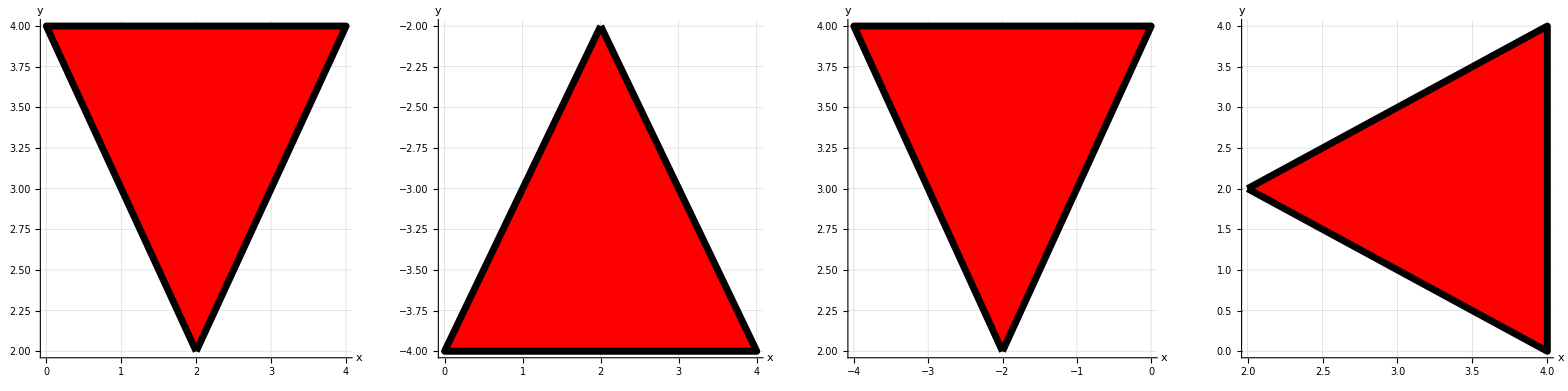

```mathematica
(* Add Point to figs *)
fig1=newGeo[{1,{{2,2},{4,4},{0,4}}}];
fig2=newGeo[{1,{{2,5},{4,6},{0,7},{3,6}}}];
fig12={fig1,fig2};
GraphicsRow[
{fig1//toGL//gr1,
ref3[fig1,{{0,1},{0,0}}]//toGL//gr1 (* Reflection in X-axis *),
ref3[fig1,{{1,0},{0,0}}]//toGL//gr1 (* Reflection in Y-axis *),
ref3[fig1,{{-1,1},{0,0}}]//toGL//gr1 (* Reflection in line Y=X *)}
]
```

```mathematica
fig1//toGL//gr1;
```

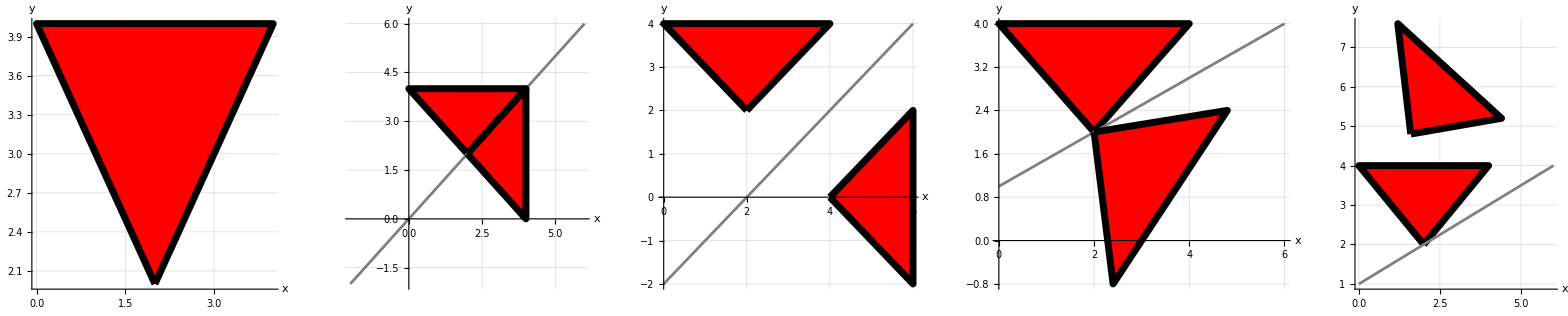

```mathematica
GraphicsRow[{
{fig1}//toGL//gr1,
{fig1,gLine[{-2,-2},{6,6},Color->Gray, Thickness->0.005],ref3[fig1,{{-1,1},{0,0}}]}//toGL//gr1,
{fig1,gLine[{0,-2},{6,4},Color->Gray, Thickness->0.005],ref3[fig1,{{-1,1},{0,-2}}]}//toGL//gr1,
{fig1,gLine[{0,1},{6,4},Color->Gray, Thickness->0.005],ref3[fig1,{{-1,2},{0,1}}]}//toGL//gr1,
{fig1,gLine[{0,1},{6,4},Color->Gray, Thickness->0.005],
ref3[ref3[fig1,{{-1,1},{0,-2}}],{{-1,2},{0,1}}]
}//toGL//gr1
}]
```

## Rot

## Tra

## Gld

## [ TBD ]